# Метод на най-малките квадрати (МНМК)

## Генериране на данни

```mathematica
xt = Table[5+t*0.13,{t,-3,15}]
```

{4.61,4.74,4.87,5.,5.13,5.26,5.39,5.52,5.65,5.78,5.91,6.04,6.17,6.3,6.43,6.56,6.69,6.82,6.95}

```mathematica
f[x_]:=2 Cos[2x-2]
yt = f[xt]
```

{1.18471,0.730649,0.22747,-0.291,-0.789909,-1.23572,-1.59847,-1.85376,-1.98445,-1.98174,-1.84582,-1.58583,-1.21923,-0.770676,-0.270319,0.24821,0.750054,1.20148,1.57214}

```mathematica
P =Length[xt]
```

19

### Визуализация

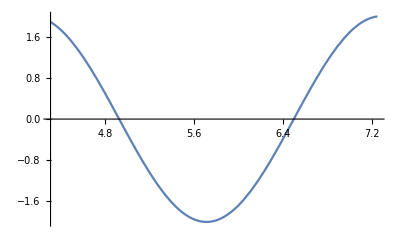

```mathematica
grf = Plot[f[x],{x,xt[[1]]-0.3,xt[[P]]+0.3}]
```

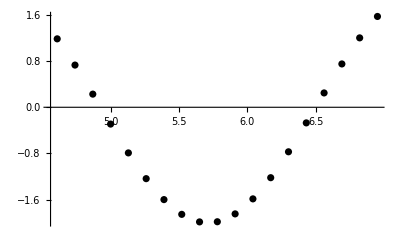

```mathematica
points = Table[{xt[[i]],yt[[i]]},{i,1,P}];
grp  = ListPlot[points, PlotStyle->Black]
```

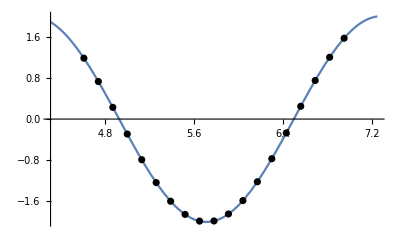

```mathematica
Show[grf, grp]
```

## Линейна регресия

### Попълваме таблицата

```mathematica
xt^2
```

{21.2521,22.4676,23.7169,25.,26.3169,27.6676,29.0521,30.4704,31.9225,33.4084,34.9281,36.4816,38.0689,39.69,41.3449,43.0336,44.7561,46.5124,48.3025}

```mathematica
yt*xt
```

{5.46153,3.46328,1.10778,-1.455,-4.05223,-6.49989,-8.61573,-10.2328,-11.2121,-11.4545,-10.9088,-9.57838,-7.52264,-4.85526,-1.73815,1.62826,5.01786,8.19409,10.9264}

#### Намиране на сумите

```mathematica
∑_(i=1)^P xt[[i]]
```

109.82

```mathematica
∑_(i=1)^P yt[[i]]
```

-9.51221

```mathematica
∑_(i=1)^P xt[[i]]^2
```

644.393

```mathematica
∑_(i=1)^P yt[[i]]*xt[[i]]
```

-52.3263

### Решаваме системата

```mathematica
A = ({{19, 109.82}, {109.82, 644.393}}); b = {-9.512,-52.326};
LinearSolve[A,b]
```

{-2.09264,0.275433}

### Съставяме полинома

```mathematica
P1[x_]:=-2.093+0.275x
```

таен коз (възможност за самопроверка)

```mathematica
Fit[points,{1,x},x]
```

-2.09324+0.275535 x

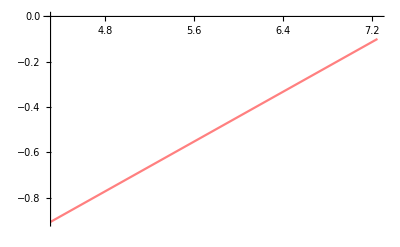

```mathematica
grP1 = Plot[P1[x],{x,xt[[1]]-0.3,xt[[P]]+0.3}, PlotStyle->Pink]
```

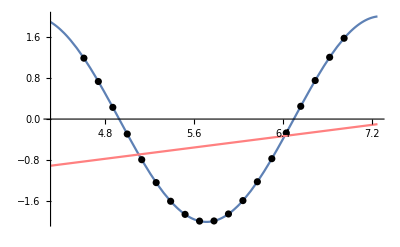

```mathematica
Show[grf, grp, grP1]
```

### Намиране на приближена стойност (апроксимация)

```mathematica
P1[4]
```

-0.993

за сравнение истинската стойност

```mathematica
f[4.]
```

1.92034

### Оценка на грешката

#### Теоретична грешка (средноквадратична)

```mathematica
√(∑_(i=1)^P (yt[[i]]-P1[xt[[i]]])^2)
```

5.02027

#### Истинска грешка

```mathematica
Abs[f[4.]-P1[4]]
```

2.91334

## Квадратична регресия

### Попълваме таблицата

```mathematica
xt^2
```

{21.2521,22.4676,23.7169,25.,26.3169,27.6676,29.0521,30.4704,31.9225,33.4084,34.9281,36.4816,38.0689,39.69,41.3449,43.0336,44.7561,46.5124,48.3025}

```mathematica
yt*xt
```

{5.46153,3.46328,1.10778,-1.455,-4.05223,-6.49989,-8.61573,-10.2328,-11.2121,-11.4545,-10.9088,-9.57838,-7.52264,-4.85526,-1.73815,1.62826,5.01786,8.19409,10.9264}

```mathematica
xt^3
```

{97.9722,106.496,115.501,125.,135.006,145.532,156.591,168.197,180.362,193.101,206.425,220.349,234.885,250.047,265.848,282.3,299.418,317.215,335.702}

```mathematica
xt^4
```

{451.652,504.793,562.491,625.,692.579,765.496,844.025,928.445,1019.05,1116.12,1219.97,1330.91,1449.24,1575.3,1709.4,1851.89,2003.11,2163.4,2333.13}

```mathematica
yt*xt^2
```

{25.1777,16.4159,5.39488,-7.275,-20.788,-34.1894,-46.4388,-56.4849,-63.3486,-66.2069,-64.4711,-57.8534,-46.4147,-30.5881,-11.1763,10.6814,33.5695,55.8837,75.9383}

#### Намиране на сумите

```mathematica
∑_(i=1)^P xt[[i]]
```

109.82

```mathematica
∑_(i=1)^P yt[[i]]
```

-9.51221

```mathematica
∑_(i=1)^P xt[[i]]^2
```

644.393

```mathematica
∑_(i=1)^P yt[[i]]*xt[[i]]
```

-52.3263

```mathematica
∑_(i=1)^P xt[[i]]^3
```

3835.95

```mathematica
∑_(i=1)^P xt[[i]]^4
```

23146.

```mathematica
∑_(i=1)^P yt[[i]]*xt[[i]]^2
```

-282.174

### Решаваме системата

```mathematica
A = ({{19, 109.82, 644.393}, {109.82, 644.393, 3835.95}, {644.393, 3835.95, 23146}}); b = {-9.512,-52.326, -282.174};
LinearSolve[A,b]
```

{80.6781,-28.8073,2.51589}

записваме в общ вид

```mathematica
A = ({{P, ∑_(i=1)^P xt[[i]], ∑_(i=1)^P xt[[i]]^2}, {∑_(i=1)^P xt[[i]], ∑_(i=1)^P xt[[i]]^2, ∑_(i=1)^P xt[[i]]^3}, {∑_(i=1)^P xt[[i]]^2, ∑_(i=1)^P xt[[i]]^3, ∑_(i=1)^P xt[[i]]^4}}); b = {∑_(i=1)^P yt[[i]],∑_(i=1)^P yt[[i]]*xt[[i]], ∑_(i=1)^P yt[[i]]*xt[[i]]^2};
a = LinearSolve[A,b]
```

{80.7295,-28.8245,2.5173}

### Съставяме полинома

```mathematica
P2[x_]:=80.678+-28.807x+2.516 x^2
```

```mathematica
P2[x_]:=a[[1]]+a[[2]]x+a[[3]] x^2
P2[x]
```

80.7295-28.8245 x+2.5173 x^2

таен коз (възможност за самопроверка)

```mathematica
Fit[points,{1,x,x^2},x]
```

80.7295-28.8245 x+2.5173 x^2

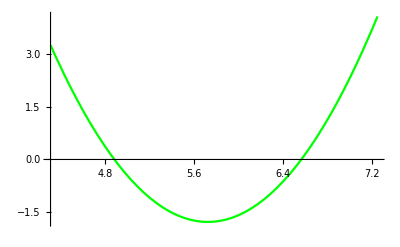

```mathematica
grP2 = Plot[P2[x],{x,xt[[1]]-0.3,xt[[P]]+0.3}, PlotStyle->Green]
```

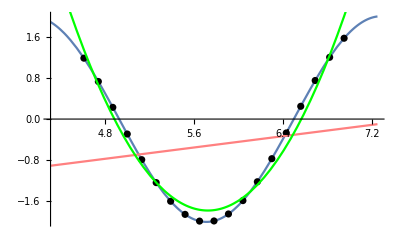

```mathematica
Show[grf, grp, grP1, grP2]
```

### Намиране на приближена стойност (апроксимация)

#### стойност извън разглеждания интервал

```mathematica
P2[4]
```

5.706

за сравнение истинската стойност

```mathematica
f[4.]
```

1.92034

#### стойност вътре в разглеждания интервал

```mathematica
P2[5.3]
```

-1.32466

за сравнение истинската стойност

```mathematica
f[5.3]
```

-1.35744

### Оценка на грешката

#### Теоретична грешка (средноквадратична)

```mathematica
√(∑_(i=1)^P (yt[[i]]-P2[xt[[i]]])^2)
```

0.806867

#### Истинска грешка

```mathematica
Abs[f[4.]-P2[4]]
```

3.78566

```mathematica
Abs[f[5.3]-P2[5.3]]
```

0.0327801

## Кубична регресия

### Попълваме таблицата

```mathematica
xt^2
```

{21.2521,22.4676,23.7169,25.,26.3169,27.6676,29.0521,30.4704,31.9225,33.4084,34.9281,36.4816,38.0689,39.69,41.3449,43.0336,44.7561,46.5124,48.3025}

```mathematica
yt*xt
```

{5.46153,3.46328,1.10778,-1.455,-4.05223,-6.49989,-8.61573,-10.2328,-11.2121,-11.4545,-10.9088,-9.57838,-7.52264,-4.85526,-1.73815,1.62826,5.01786,8.19409,10.9264}

```mathematica
xt^3
```

{97.9722,106.496,115.501,125.,135.006,145.532,156.591,168.197,180.362,193.101,206.425,220.349,234.885,250.047,265.848,282.3,299.418,317.215,335.702}

```mathematica
xt^4
```

{451.652,504.793,562.491,625.,692.579,765.496,844.025,928.445,1019.05,1116.12,1219.97,1330.91,1449.24,1575.3,1709.4,1851.89,2003.11,2163.4,2333.13}

```mathematica
yt*xt^2
```

{25.1777,16.4159,5.39488,-7.275,-20.788,-34.1894,-46.4388,-56.4849,-63.3486,-66.2069,-64.4711,-57.8534,-46.4147,-30.5881,-11.1763,10.6814,33.5695,55.8837,75.9383}

допълваме необходимото

#### Намиране на сумите

```mathematica
∑_(i=1)^P xt[[i]]
```

109.82

```mathematica
∑_(i=1)^P yt[[i]]
```

-9.51221

```mathematica
∑_(i=1)^P xt[[i]]^2
```

644.393

```mathematica
∑_(i=1)^P yt[[i]]*xt[[i]]
```

-52.3263

```mathematica
∑_(i=1)^P xt[[i]]^3
```

3835.95

```mathematica
∑_(i=1)^P xt[[i]]^4
```

23146.

```mathematica
∑_(i=1)^P yt[[i]]*xt[[i]]^2
```

-282.174

допълваме необходимото

### Решаваме системата

записваме в общ вид

```mathematica
A = ({{P, ∑_(i=1)^P xt[[i]], ∑_(i=1)^P xt[[i]]^2, ∑_(i=1)^P xt[[i]]^3}, {∑_(i=1)^P xt[[i]], ∑_(i=1)^P xt[[i]]^2, ∑_(i=1)^P xt[[i]]^3, ∑_(i=1)^P xt[[i]]^4}, {∑_(i=1)^P xt[[i]]^2, ∑_(i=1)^P xt[[i]]^3, ∑_(i=1)^P xt[[i]]^4, ∑_(i=1)^P xt[[i]]^5}, {∑_(i=1)^P xt[[i]]^3, ∑_(i=1)^P xt[[i]]^4, ∑_(i=1)^P xt[[i]]^5, ∑_(i=1)^P xt[[i]]^6}}); b = {∑_(i=1)^P yt[[i]],∑_(i=1)^P yt[[i]]*xt[[i]], ∑_(i=1)^P yt[[i]]*xt[[i]]^2, ∑_(i=1)^P yt[[i]]*xt[[i]]^3};
a = LinearSolve[A,b]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{19.,109.82,644.393,3835.95},{109.82,644.393,3835.95,23146.},{«1»},{3835.95,23146.,141427.,874141.}} may contain significant numerical errors.

{128.634,-54.1524,6.93941,-0.255023}

### Съставяме полинома

```mathematica
P3[x_]:=a[[1]]+a[[2]]x+a[[3]] x^2+a[[4]] x^3
P3[x]
```

128.634-54.1524 x+6.93941 x^2-0.255023 x^3

таен коз (възможност за самопроверка)

```mathematica
Fit[points,{1,x,x^2,x^3},x]
```

128.634-54.1524 x+6.93941 x^2-0.255023 x^3

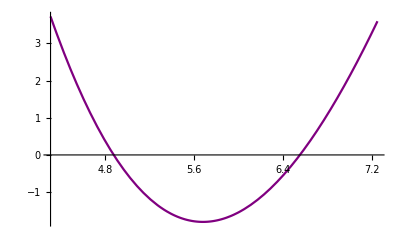

```mathematica
grP3 = Plot[P3[x],{x,xt[[1]]-0.3,xt[[P]]+0.3}, PlotStyle->Purple]
```

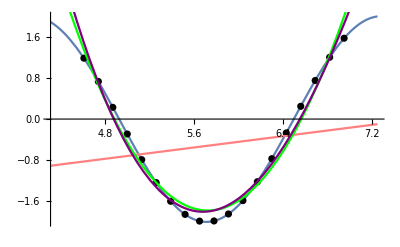

```mathematica
Show[grf, grp, grP1, grP2, grP3]
```

### Намиране на приближена стойност (апроксимация)

#### стойност извън разглеждания интервал

```mathematica
P3[4]
```

6.73399

за сравнение истинската стойност

```mathematica
f[4.]
```

1.92034

#### стойност вътре в разглеждания интервал

```mathematica
P3[5.3]
```

-1.41228

за сравнение истинската стойност

```mathematica
f[5.3]
```

-1.35744

### Оценка на грешката

#### Теоретична грешка (средноквадратична)

```mathematica
√(∑_(i=1)^P (yt[[i]]-P3[xt[[i]]])^2)
```

0.744355

#### Истинска грешка

```mathematica
Abs[f[4.]-P3[4]]
```

4.81364

```mathematica
Abs[f[5.3]-P3[5.3]]
```

0.0548399